```mathematica
(*Definitions*)
β = 800;
z = 2;
U = 3;
μ = U/2;
t = 1/(√z);
ω[n_Integer]=π*(2n+1)/β;
s[ζ_] := Sign[Im[ζ]];
(*Densities and Hilbert transforms*)
Subscript[ρ, bethe][ϵ_Real] := Piecewise[{{(√(4 t^2-ϵ^2))/(2π t^2),Abs[ϵ]<2t}},0];
Subscript[D̃, bethe][ζ_] := (ζ-Sign[Im[ζ]]*√(ζ^2-4 t^2))/(2 t^2);
Subscript[ρ, SC][ϵ_Real] := Exp[-ϵ^2/(2 t^2)]/(√(2π)t);
Subscript[D̃, SC][ζ_] := -ⅈ*Sign[Im[ζ]] √π ⅇ^(-ζ^2)Erfc[-ⅈ*Sign[Im[ζ]]*ζ];
Subscript[ρ, lorentz][ϵ_Real] :=t/(π(ϵ^2+t^2));
Subscript[D̃, lorentz][ζ_] := 1/(ζ+ⅈ*t*s[ζ]);

(*Green's functions*)
Subscript[G, 0,ω][ζ_]:=Simplify[Integrate[(Subscript[ρ, bethe][ϵ])/(ζ-ϵ),{ϵ,-2t,2t}],ζ∉Reals];
Subscript[G3, 0,ω][ζ_] := (ζ-√(ζ-2)*√(ζ+2))/(2*t^2);
Subscript[G, 0,τ][τ_Real]:=NSum[Exp[-ⅈ*ω[n]*τ]/β*Subscript[G, 0,ω][ⅈ*ω[n]],{n,-∞,∞}];
Subscript[G2, 0,τ][τ_Real]:=NSum[Exp[-ⅈ*ω[n]*τ]/β*Subscript[D̃, bethe][ⅈ*ω[n] +μ],{n,-∞,∞}];
Subscript[N, ω] = 2^8; (*number of Matsubara frequencies*)
Subscript[N, τ]= 2^8;(*number of time steps. Equal to Subscript[N, ω] for FFT.*)
Subscript[n, min]= -Subscript[N, ω]/2; (*Subscript[N, τ]=(2π)/(δt*δω); see triqs fourier impl notes*)
Subscript[n, max]= Subscript[N, ω]/2-1;
δt = β/Subscript[N, τ];
δω = (2π)/β;
```

```mathematica
(*Test for numerical computations*)
Subscript[dataG, ω] = ParallelTable[Subscript[D̃, bethe][ⅈ*ω[n]],{n,Subscript[n, min],Subscript[n, max],1}];
SetSharedVariable[j];
(* faster than Sum[Exp[-ⅈω[n]τ]/β Subscript[D̃, bethe][ⅈω[n]+μ]]*)
Subscript[dataG, τ]=Monitor[ParallelTable[j=x;Sum[Exp[-ⅈ*π*(2n+1)/β*x]/β*(ⅈ*π*(2n+1)/β+μ-√((ⅈ*π*(2n+1)/β+μ)^2-4 t^2))/(2 t^2),{n,0,Subscript[n, max],1}] ,{x,δt/2 ,β-δt/2 ,δt }],j];

Subscript[xlist, ω] = Range[Subscript[n, min],Subscript[n, max],1];
Subscript[data, ω]= Transpose@{Subscript[xlist, ω],Im[Subscript[dataG, ω]]};
Subscript[xlist, τ]=Range[δt/2,β-δt/2,δt ];
Subscript[data, τ]= Transpose@{Subscript[xlist, τ],Re[Subscript[dataG, τ]]};
ListPlot[Subscript[data, ω]]
ListPlot[Subscript[data, τ]]
```

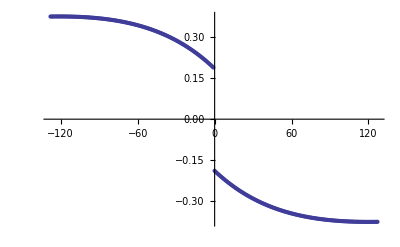

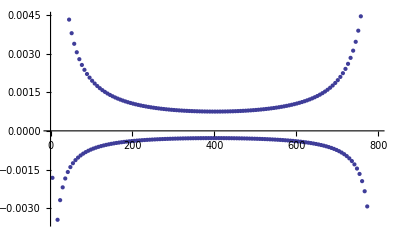

```mathematica
(*Test for SC *)
SetSharedVariable[j];
Subscript[dataG, ω,SC] = ParallelTable[Subscript[D̃, SC][ⅈ*ω[n]+μ]//N,{n,Subscript[n, min],Subscript[n, max],1}];
Subscript[dataG, τ]= Monitor[ParallelTable[j=x;Sum[Exp[ⅈ*π*(2n+1)/β*x]/β*Subscript[D̃, SC][ⅈ*ω[n]+μ]//N,{n,Subscript[n, min],Subscript[n, max],1}] ,{x,δt/2 ,β-δt/2 ,δt }],j];
Subscript[xlist, ω] = Range[Subscript[n, min],Subscript[n, max],1];
Subscript[data, ω]= Transpose@{Subscript[xlist, ω],Im[Subscript[dataG, ω,SC]]};
Subscript[xlist, τ]=Range[δt/2,β-δt/2,δt ];
Subscript[data, τ]= Transpose@{Subscript[xlist, τ],Re[Subscript[dataG, τ]]};
ListPlot[Subscript[data, ω]]
ListPlot[Subscript[data, τ]]
```

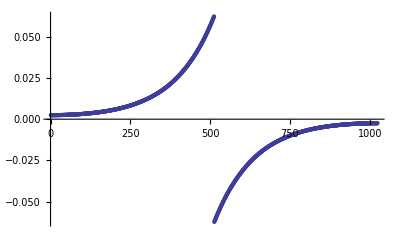

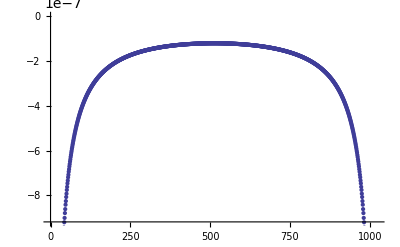

```mathematica
(*Test for FFT *)
Subscript[N, ω] = 1024; (*number of Matsubara frequencies*)
Subscript[N, τ]=1024;(*number of time steps. Equal to Subscript[N, ω] for FFT.*)
Subscript[n, min]= -Subscript[N, ω]/2; (*Subscript[N, τ]=(2π)/(δt*δω); see triqs fourier impl notes*)
Subscript[n, max]= Subscript[N, ω]/2-1;
δt = β/Subscript[N, τ];
δω = (2π)/β;
(*Subscript[dataG, ω] = ParallelTable[(ⅈ*π*(2n+1)/β-Sign[π*(2n+1)/β]*√(-(π*(2n+1)/β)^2-4 t^2))/(2 t^2),{n,Subscript[n, min],Subscript[n, max],1}];
Subscript[dataG, τ]=Monitor[ParallelTable[j=x;MapIndexed[Exp[-ⅈ*π*(2*(First[Subscript[n, min]+#1-1])+1)/β*x]/β*#1&,Subscript[dataG, ω] ] ,{x,δt/2 ,β-δt/2 ,δt }],j];*)

Subscript[f̃, k]=MapIndexed[#1*Exp[ⅈ*ω[Subscript[n, min]]*(First[#2]*δt-δt/2)]&,Subscript[dataG, τ]];
ListPlot[Im[MapIndexed[δt*#1*Exp[ⅈ*(δt/2)*(ω[Subscript[n, min]+First[#2]-1]-ω[Subscript[n, min]])]&,Fourier[Subscript[f̃, k]]]]]
Subscript[f, n]=MapIndexed[#1/β*Exp[-ⅈ*(δt/2)*ω[Subscript[n, min]+First[#2]-1]]&,Subscript[dataG, ω]];
ListPlot[Re[MapIndexed[#1*Exp[-ⅈ*ω[Subscript[n, min]]*(First[#2]*δt-(δt/2))]&,InverseFourier[Subscript[f, n]]]]]
```

```mathematica
tmp = ParallelTable[(ⅈ*π*(2n+1)/β-Sign[π*(2n+1)/β]*√(-(π*(2n+1)/β)^2-4 t^2))/(2 t^2),{n,Subscript[n, min],Subscript[n, max],1}];
tmp2=Monitor[ParallelTable[j=x;MapIndexed[Exp[-ⅈ*π*(2*(First[Subscript[n, min]+#1-1])+1)/β*x]/β*#1&,tmp ],{x,δt/2 ,β-δt/2 ,δt }],j];
```

$Aborted

```mathematica
Subscript[f̃, k]=MapIndexed[#1*Exp[ⅈ*ω[Subscript[n, min]]*(-δt/2+First[#2]*δt)]&,Subscript[dataG, τ]];
ListPlot[Im[MapIndexed[δt*#1*Exp[ⅈ*(δt/2)*(ω[Subscript[n, min]+First[#2]-1]-ω[Subscript[n, min]])]&,Fourier[Subscript[f̃, k]]]]]
Subscript[f, n]=MapIndexed[#1/β*Exp[-ⅈ*(δt/2)*ω[Subscript[n, min]+First[#2]-1]]&,Subscript[dataG, ω]];
ListPlot[Re[MapIndexed[#1*Exp[-ⅈ*ω[Subscript[n, min]]*(First[#2]*δt-(δt/2))]&,InverseFourier[Subscript[f, n]]]]]
```

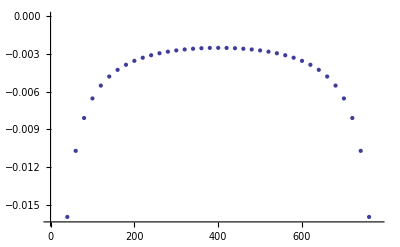

```mathematica
(*non expanded version*)
Subscript[G2, τ]= Monitor[Table[Re[Subscript[G2, 0,τ][x]],{x,20,800-20,20}],x];
xlist=Range[20,800-20,20];
data = Transpose@{xlist,Subscript[G, τ]};
ListPlot[data]
```

```mathematica
(*Subscript[G, l,τ]= Monitor[Table[Re[Subscript[G, 0,τ][x]],{x,20,800-20,20}],x];
xlist=Range[20,800-20,20];
data = Transpose@{xlist,Subscript[G, τ]};
ListPlot[data]*)
```